```mathematica
humhum[primeList_] := (Sum[Log[(p + 1)/(2*p)]/Log[p], {p, primeList}] + 1) / Sum[PartitionsP[(p+1)/2], {p, primeList}]
```

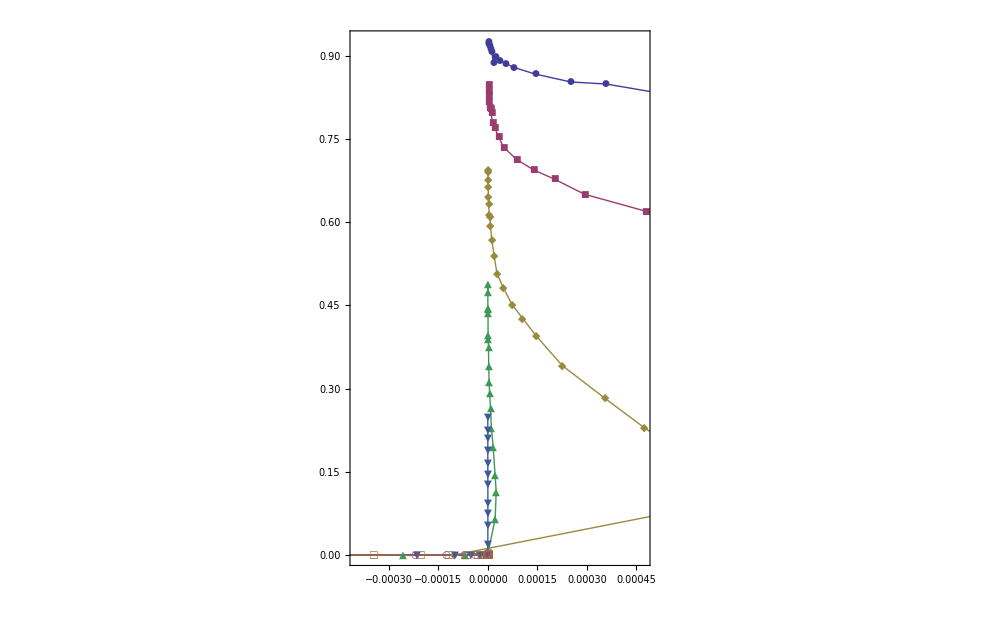

```mathematica
ListPlot[Table[Map[{humhum[#[[1]]],#[[2]]}&, Select[Flatten[klm5,1],Length[#[[1]]]== l &]], {l,2,8}],  PlotMarkers->Automatic, Joined->True, ImageSize->1000, GridLines->{{1/Sqrt[4],1/Sqrt[6],1/Sqrt[8],1/5,1/6},Automatic}, Frame->True]
```

```mathematica
klm5={{{{3,5},33593/100001},{{3,5,7},559/18750},{{3,5,7,11},1/37550},{{3,5,7,11,13},2/100001},{{3,5,7,11,13,17},2/100001},{{3,5,7,11,13,17,19},2/100001},{{3,5,7,11,13,17,19,23},2/100001}},{{{5,7},44714/100001},{{5,7,11},50114/300001},{{5,7,11,13},8/100001},{{5,7,11,13,17},5/100001},{{5,7,11,13,17,19},4/100001},{{5,7,11,13,17,19,23},4/100001},{{5,7,11,13,17,19,23,29},3/100001}},{{{7,11},55106/100001},{{7,11,13},80936/300001},{{7,11,13,17},28/73707},{{7,11,13,17,19},12/100001},{{7,11,13,17,19,23},5/40001},{{7,11,13,17,19,23,29},4/40001},{{7,11,13,17,19,23,29,31},2/21235}},{{{11,13},61681/100001},{{11,13,17},110523/300001},{{11,13,17,19},9761/111217},{{11,13,17,19,23},7/100001},{{11,13,17,19,23,29},6/40001},{{11,13,17,19,23,29,31},6/40001},{{11,13,17,19,23,29,31,37},6/40001}},{{{13,17},67024/100001},{{13,17,19},127206/300001},{{13,17,19,23},7738/50001},{{13,17,19,23,29},14/40001},{{13,17,19,23,29,31},7/40001},{{13,17,19,23,29,31,37},7/40001},{{13,17,19,23,29,31,37,41},7/40001}},{{{17,19},70308/100001},{{17,19,23},143739/300001},{{17,19,23,29},2084/9091},{{17,19,23,29,31},59/100001},{{17,19,23,29,31,37},9/49274},{{17,19,23,29,31,37,41},9/40001},{{17,19,23,29,31,37,41,43},9/40001}},{{{19,23},42848/58167},{{19,23,29},12337/23077},{{19,23,29,31},15919/56265},{{19,23,29,31,37},244/40001},{{19,23,29,31,37,41},14/40001},{{19,23,29,31,37,41,43},10/40001},{{19,23,29,31,37,41,43,47},10/40001}},{{{23,29},12937/16667},{{23,29,31},173627/300001},{{23,29,31,37},17081/50001},{{23,29,31,37,41},2611/40001},{{23,29,31,37,41,43},18/40001},{{23,29,31,37,41,43,47},12/40001},{{23,29,31,37,41,43,47,53},12/40001}},{{{29,31},5711/7143},{{29,31,37},185974/300001},{{29,31,37,41},941/2381},{{29,31,37,41,43},352/3077},{{29,31,37,41,43,47},1/2353},{{29,31,37,41,43,47,53},16/40001},{{29,31,37,41,43,47,53,59},15/40001}},{{{31,37},40928/50001},{{31,37,41},195055/300001},{{31,37,41,43},21347/50001},{{31,37,41,43,47},5815/40001},{{31,37,41,43,47,53},28/40001},{{31,37,41,43,47,53,59},16/40001},{{31,37,41,43,47,53,59,61},16/40001}},{{{37,41},13912/16667},{{37,41,43},203339/300001},{{37,41,43,47},22576/50001},{{37,41,43,47,53},7779/40001},{{37,41,43,47,53,59},48/40001},{{37,41,43,47,53,59,61},21/40001},{{37,41,43,47,53,59,61,67},21/40001}},{{{41,43},42436/50001},{{41,43,47},208191/300001},{{41,43,47,53},8040/16667},{{41,43,47,53,59},9205/40001},{{41,43,47,53,59,61},56/40001},{{41,43,47,53,59,61,67},24/40001},{{41,43,47,53,59,61,67,71},22/40001}},{{{43,47},14206/16667},{{43,47,53},214073/300001},{{43,47,53,59},25366/50001},{{43,47,53,59,61},10615/40001},{{43,47,53,59,61,67},132/40001},{{43,47,53,59,61,67,71},28/40001},{{43,47,53,59,61,67,71,73},22/40001}},{{{47,53},43336/50001},{{47,53,59},220498/300001},{{47,53,59,61},26993/50001},{{47,53,59,61,67},11676/40001},{{47,53,59,61,67,71},63/3077},{{47,53,59,61,67,71,73},28/40001},{{47,53,59,61,67,71,73,79},28/40001}},{{{53,59},14648/16667},{{53,59,61},17394/23077},{{53,59,61,67},9468/16667},{{53,59,61,67,71},12527/40001},{{53,59,61,67,71,73},167/3077},{{53,59,61,67,71,73,79},50/40001},{{53,59,61,67,71,73,79,83},27/40001}},{{{59,61},44290/50001},{{59,61,67},231216/300001},{{59,61,67,71},9888/16667},{{59,61,67,71,73},13643/40001},{{59,61,67,71,73,79},3047/40001},{{59,61,67,71,73,79,83},13/11974},{{59,61,67,71,73,79,83,89},30/40001}},{{{61,67},44585/50001},{{61,67,71},233549/300001},{{61,67,71,73},30508/50001},{{61,67,71,73,79},15051/40001},{{61,67,71,73,79,83},3786/40001},{{61,67,71,73,79,83,89},50/40001},{{61,67,71,73,79,83,89,97},41/40001}},{{{67,71},44924/50001},{{67,71,73},239448/300001},{{67,71,73,79},30676/50001},{{67,71,73,79,83},15585/40001},{{67,71,73,79,83,89},5146/40001},{{67,71,73,79,83,89,97},94/40001},{{67,71,73,79,83,89,97,101},40/40001}},{{{71,73},44356/50001},{{71,73,79},241413/300001},{{71,73,79,83},10543/16667},{{71,73,79,83,89},15877/40001},{{71,73,79,83,89,97},347/2353},{{71,73,79,83,89,97,101},48/40001},{{71,73,79,83,89,97,101,103},40/40001}},{{{73,79},2161/2381},{{73,79,83},242155/300001},{{73,79,83,89},10754/16667},{{73,79,83,89,97},17785/40001},{{73,79,83,89,97,101},6644/40001},{{73,79,83,89,97,101,103},44/40001},{{73,79,83,89,97,101,103,107},40/40001}},{{{79,83},15215/16667},{{79,83,89},245281/300001},{{79,83,89,97},11071/16667},{{79,83,89,97,101},17491/40001},{{79,83,89,97,101,103},7603/40001},{{79,83,89,97,101,103,107},6/3077},{{79,83,89,97,101,103,107,109},56/40001}},{{{83,89},45896/50001},{{83,89,97},248357/300001},{{83,89,97,101},33862/50001},{{83,89,97,101,103},17860/40001},{{83,89,97,101,103,107},8435/40001},{{83,89,97,101,103,107,109},69/40001},{{83,89,97,101,103,107,109,113},54/40001}},{{{89,97},46121/50001},{{89,97,101},250996/300001},{{89,97,101,103},33653/48706},{{89,97,101,103,107},19529/40001},{{89,97,101,103,107,109},9017/40001},{{89,97,101,103,107,109,113},118/40001},{{89,97,101,103,107,109,113,127},59/40001}},{{{97,101},6613/7143},{{97,101,103},254327/300001},{{97,101,103,107},27767/40001},{{97,101,103,107,109},19004/40001},{{97,101,103,107,109,113},9989/40001},{{97,101,103,107,109,113,127},200/40001},{{97,101,103,107,109,113,127,131},7/2353}}}
```

{{{{3,5},33593/100001},{{3,5,7},559/18750},{{3,5,7,11},1/37550},{{3,5,7,11,13},2/100001},{{3,5,7,11,13,17},2/100001},{{3,5,7,11,13,17,19},2/100001},{{3,5,7,11,13,17,19,23},2/100001}},{{{5,7},44714/100001},{{5,7,11},50114/300001},{{5,7,11,13},8/100001},{{5,7,11,13,17},5/100001},{{5,7,11,13,17,19},4/100001},{{5,7,11,13,17,19,23},4/100001},{{5,7,11,13,17,19,23,29},3/100001}},{{{7,11},55106/100001},{{7,11,13},80936/300001},{{7,11,13,17},28/73707},{{7,11,13,17,19},12/100001},{{7,11,13,17,19,23},5/40001},{{7,11,13,17,19,23,29},4/40001},{{7,11,13,17,19,23,29,31},2/21235}},{{{11,13},61681/100001},{{11,13,17},110523/300001},{{11,13,17,19},9761/111217},{{11,13,17,19,23},7/100001},{{11,13,17,19,23,29},6/40001},{{11,13,17,19,23,29,31},6/40001},{{11,13,17,19,23,29,31,37},6/40001}},{{{13,17},67024/100001},{{13,17,19},127206/300001},{{13,17,19,23},7738/50001},{{13,17,19,23,29},14/40001},{{13,17,19,23,29,31},7/40001},{{13,17,19,23,29,31,37},7/40001},{{13,17,19,23,29,31,37,41},7/40001}},{{{17,19},70308/100001},{{17,19,23},143739/300001},{{17,19,23,29},2084/9091},{{17,19,23,29,31},59/100001},{{17,19,23,29,31,37},9/49274},{{17,19,23,29,31,37,41},9/40001},{{17,19,23,29,31,37,41,43},9/40001}},{{{19,23},42848/58167},{{19,23,29},12337/23077},{{19,23,29,31},15919/56265},{{19,23,29,31,37},244/40001},{{19,23,29,31,37,41},14/40001},{{19,23,29,31,37,41,43},10/40001},{{19,23,29,31,37,41,43,47},10/40001}},{{{23,29},12937/16667},{{23,29,31},173627/300001},{{23,29,31,37},17081/50001},{{23,29,31,37,41},2611/40001},{{23,29,31,37,41,43},18/40001},{{23,29,31,37,41,43,47},12/40001},{{23,29,31,37,41,43,47,53},12/40001}},{{{29,31},5711/7143},{{29,31,37},185974/300001},{{29,31,37,41},941/2381},{{29,31,37,41,43},352/3077},{{29,31,37,41,43,47},1/2353},{{29,31,37,41,43,47,53},16/40001},{{29,31,37,41,43,47,53,59},15/40001}},{{{31,37},40928/50001},{{31,37,41},195055/300001},{{31,37,41,43},21347/50001},{{31,37,41,43,47},5815/40001},{{31,37,41,43,47,53},28/40001},{{31,37,41,43,47,53,59},16/40001},{{31,37,41,43,47,53,59,61},16/40001}},{{{37,41},13912/16667},{{37,41,43},203339/300001},{{37,41,43,47},22576/50001},{{37,41,43,47,53},7779/40001},{{37,41,43,47,53,59},48/40001},{{37,41,43,47,53,59,61},21/40001},{{37,41,43,47,53,59,61,67},21/40001}},{{{41,43},42436/50001},{{41,43,47},208191/300001},{{41,43,47,53},8040/16667},{{41,43,47,53,59},9205/40001},{{41,43,47,53,59,61},56/40001},{{41,43,47,53,59,61,67},24/40001},{{41,43,47,53,59,61,67,71},22/40001}},{{{43,47},14206/16667},{{43,47,53},214073/300001},{{43,47,53,59},25366/50001},{{43,47,53,59,61},10615/40001},{{43,47,53,59,61,67},132/40001},{{43,47,53,59,61,67,71},28/40001},{{43,47,53,59,61,67,71,73},22/40001}},{{{47,53},43336/50001},{{47,53,59},220498/300001},{{47,53,59,61},26993/50001},{{47,53,59,61,67},11676/40001},{{47,53,59,61,67,71},63/3077},{{47,53,59,61,67,71,73},28/40001},{{47,53,59,61,67,71,73,79},28/40001}},{{{53,59},14648/16667},{{53,59,61},17394/23077},{{53,59,61,67},9468/16667},{{53,59,61,67,71},12527/40001},{{53,59,61,67,71,73},167/3077},{{53,59,61,67,71,73,79},50/40001},{{53,59,61,67,71,73,79,83},27/40001}},{{{59,61},44290/50001},{{59,61,67},231216/300001},{{59,61,67,71},9888/16667},{{59,61,67,71,73},13643/40001},{{59,61,67,71,73,79},3047/40001},{{59,61,67,71,73,79,83},13/11974},{{59,61,67,71,73,79,83,89},30/40001}},{{{61,67},44585/50001},{{61,67,71},233549/300001},{{61,67,71,73},30508/50001},{{61,67,71,73,79},15051/40001},{{61,67,71,73,79,83},3786/40001},{{61,67,71,73,79,83,89},50/40001},{{61,67,71,73,79,83,89,97},41/40001}},{{{67,71},44924/50001},{{67,71,73},239448/300001},{{67,71,73,79},30676/50001},{{67,71,73,79,83},15585/40001},{{67,71,73,79,83,89},5146/40001},{{67,71,73,79,83,89,97},94/40001},{{67,71,73,79,83,89,97,101},40/40001}},{{{71,73},44356/50001},{{71,73,79},241413/300001},{{71,73,79,83},10543/16667},{{71,73,79,83,89},15877/40001},{{71,73,79,83,89,97},347/2353},{{71,73,79,83,89,97,101},48/40001},{{71,73,79,83,89,97,101,103},40/40001}},{{{73,79},2161/2381},{{73,79,83},242155/300001},{{73,79,83,89},10754/16667},{{73,79,83,89,97},17785/40001},{{73,79,83,89,97,101},6644/40001},{{73,79,83,89,97,101,103},44/40001},{{73,79,83,89,97,101,103,107},40/40001}},{{{79,83},15215/16667},{{79,83,89},245281/300001},{{79,83,89,97},11071/16667},{{79,83,89,97,101},17491/40001},{{79,83,89,97,101,103},7603/40001},{{79,83,89,97,101,103,107},6/3077},{{79,83,89,97,101,103,107,109},56/40001}},{{{83,89},45896/50001},{{83,89,97},248357/300001},{{83,89,97,101},33862/50001},{{83,89,97,101,103},17860/40001},{{83,89,97,101,103,107},8435/40001},{{83,89,97,101,103,107,109},69/40001},{{83,89,97,101,103,107,109,113},54/40001}},{{{89,97},46121/50001},{{89,97,101},250996/300001},{{89,97,101,103},33653/48706},{{89,97,101,103,107},19529/40001},{{89,97,101,103,107,109},9017/40001},{{89,97,101,103,107,109,113},118/40001},{{89,97,101,103,107,109,113,127},59/40001}},{{{97,101},6613/7143},{{97,101,103},254327/300001},{{97,101,103,107},27767/40001},{{97,101,103,107,109},19004/40001},{{97,101,103,107,109,113},9989/40001},{{97,101,103,107,109,113,127},200/40001},{{97,101,103,107,109,113,127,131},7/2353}}}